Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

2.5

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

1819.48

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

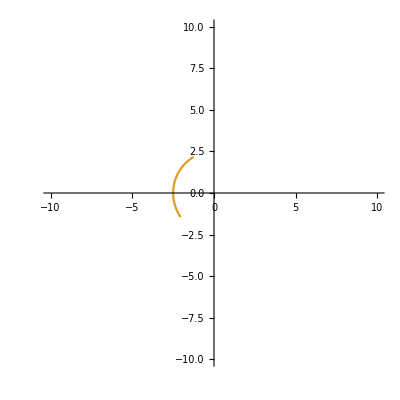

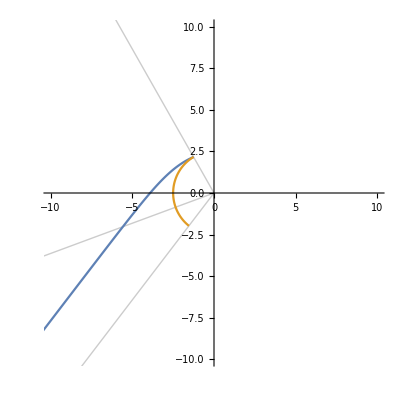

```mathematica
Clear["Global`*"]

trajectoryR:=Sqrt[rg^2(1-Cos[psi-inclinationAngle-(emissionAngle)])^2/(4(1+Cos[psi-inclinationAngle-(emissionAngle)])^2)+b^2/Sin[psi-inclinationAngle-(emissionAngle)]^2]-rg(1-Cos[psi-inclinationAngle-(emissionAngle)])/(2(1+Cos[psi-inclinationAngle-(emissionAngle)]));

b:=R Sin[alpha]/Sqrt[1-rg/R]

R:=2.5rg;
alpha:=1.221;
rg:=1
emissionAngle:=Pi/2+Pi/6;

inclinationAngle:=t/.Solve[1-Cos[alpha]==(1-Cos[t])(1-rg/R),t][[2]];

Print[trajectoryR/.psi->emissionAngle]
Print[trajectoryR/.psi->emissionAngle+0.999inclinationAngle]

p1=PolarPlot[{trajectoryR,R},{psi,emissionAngle,emissionAngle+inclinationAngle}, PlotRange->10,PolarGridLines->{{inclinationAngle+emissionAngle,alpha+emissionAngle,emissionAngle},{}}]

(*inclinationAngle:=t/.Solve[1-Cos[alpha]==(1-Cos[t])(1-rg/R),t][[2]];
p2=PolarPlot[{trajectoryR,R},{psi,emissionAngle,emissionAngle+inclinationAngle}, PlotRange->10,PolarGridLines->{{inclinationAngle+emissionAngle,alpha+emissionAngle,emissionAngle},{}}];
(*p2=PolarPlot[R,{psi,-Pi,Pi}, PlotRange->5,PlotStyle->Yellow];*)
Show[p1,p2]*)
```

```mathematica
(*trajectoryPsi/.r->10000000000*)
trajectoryR/.psi->0.01
psi/.Solve[1-Cos[alpha]==(1-Cos[psi])(1-rg/R),psi]
```

321.116

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{-2.09319,2.09319}

```mathematica
ArcCos[0.1]
Cos[1.57]
```

1.47063

0.000796327

```mathematica
Integrate[Tan[x],x]
```

-Log[Cos[x]]

```mathematica
70/90*Pi/2.
```

1.22173